## Computer Project 1 Due Sunday February 10, by midnight AMS 513 Spring 2019

Assignment: 
1) Execute the lines of code below by putting the cursor in the cell and pressing shift-enter
2) Answer Question 1 
3) Answer Question 2 
4) Save your completed notebook in a file with your name on it, e.g. MyName_Project1_AMS513.nb and submit online in the BlackBoard.

The function H_n(ω) is the number of heads occurring in the first n tosses of an infinite coin toss sequence outcome ω∈Ω_∞.

We start by defining a function to generate a coin toss sequence, 0 is a tail, 1 is a head.
The underscore suffix in howMany means that this is a dummy argument to the module.

Part 1

```mathematica
coinTosses[howMany_]:=Module[{tosses},
tosses= RandomInteger[{0,1},howMany]
];
```

The function (H_n(ω))/nis like an estimate of the probability of getting an H based on the first n tosses of a realized ω..
To define it, first define the probability based on a given fixed value of n.
Note that the sequence here is assumed to be at least n tosses long.

```mathematica
empiricalHeadProbabilitySlow[n_,sequence_]:=N[Length[Select[Take[sequence,n],OddQ]]/n];
```

The (H_n(ω))/n function as a sequence indexed by n:

```mathematica
empiricalHeadProbabilitySLOW[howMany_]:=Module[{toss},
toss=coinTosses[howMany];
{toss,Table[empiricalHeadProbabilitySlow[i,toss],{i,howMany}]}];
```

Or, another way to compute this:

```mathematica
empiricalHeadProbabilityFAST[seqLength_]:=N[Rest[FoldList[Plus,0,coinTosses[seqLength]]]/Range[seqLength]];
```

SLOW Run:

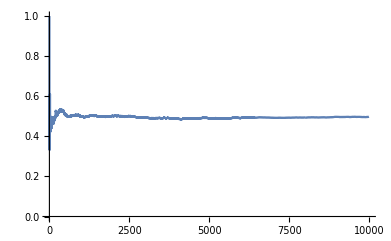

1 run(s) took 8.73438 seconds

```mathematica
nRuns=1;
nTosses=10000;
{time,{tosses,ratios}}=Timing[Transpose[Table[empiricalHeadProbabilitySLOW[nTosses],{nRuns}]]];
ListPlot[ratios,Joined->True,PlotRange->{0,1}]
Print[ToString[nRuns]<>" run(s) took "<>ToString[time]<>" seconds"]
```

FAST Run:

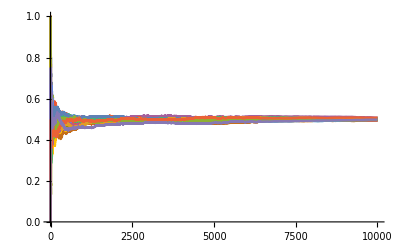

20 run(s) took 0.109375 seconds

```mathematica
nRuns=20;
nTosses=10000;
{time,ratios}=Timing[Table[empiricalHeadProbabilityFAST[nTosses],{nRuns}]];
ListPlot[ratios,Joined->True,PlotRange->{0,1}]
Print[ToString[nRuns]<>" run(s) took "<>ToString[time]<>" seconds"]
```

Question 1:

(A) How much faster is the FAST method over the SLOW method for nTosses = 100, 1000, 10000, 20000?

ANSWER:

(B) Explain why the FAST method is so much faster.

ANSWER: The FAST method uses FoldList which iterates the solution.  The SLOW method does many calculations over and over because they are repeated for each toss in the sequence.

Part 2

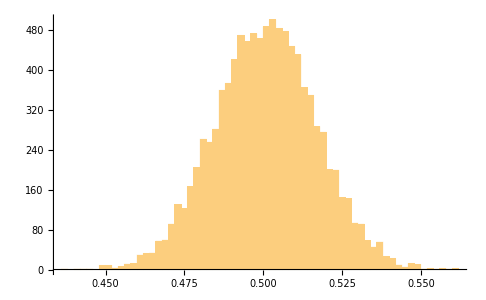

```mathematica
nTosses=1000;
nTrials=10000;
probabilityTable=Table[Last[empiricalHeadProbabilityFAST[nTosses]],{nTrials}];
Histogram[probabilityTable,50]
```

```mathematica
nTosses=1000;
nTrials=10000;
probabilityTable=Table[empiricalHeadProbabilityFAST[nTosses],{nTrials}];
```

```mathematica
kurt=Kurtosis[probabilityTable];
skew=Skewness[probabilityTable];
sdev=StandardDeviation[probabilityTable];
mean=Mean[probabilityTable];
```

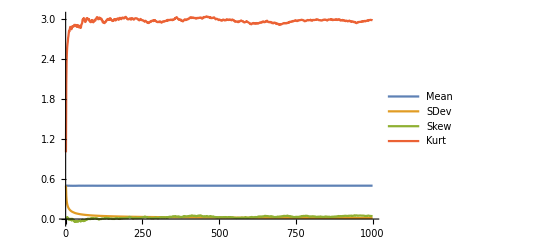

```mathematica
ListPlot[{mean,sdev,skew,kurt},Joined->True,PlotLegends->{"Mean","SDev","Skew","Kurt"}]
```

A boolean function returning a sequence containing n booleans, true when the sequence is in A_(n,m)={ω:|(H_n(ω))/n-1/2|≤1/m}.  The input to this function is the empirical probability sequence.

```mathematica
seqAnm[m_,seq_]:=Thread[Function[{a,b},a<b][Abs[seq-0.5],1/m]];
```

Here is an example with 20 tosses and m=20.

```mathematica
empiricalHeadProb=empiricalHeadProbabilityFAST[20]
seqAnm[20,empiricalHeadProb]
```

{0.,0.,0.333333,0.5,0.4,0.5,0.428571,0.5,0.555556,0.5,0.454545,0.416667,0.384615,0.357143,0.4,0.4375,0.470588,0.5,0.473684,0.5}

{False,False,False,True,False,True,False,True,False,True,True,False,False,False,False,False,True,True,True,True}

Plotting the data, the orange dots indicate whether or not the sequence is in A_(n,m) for the given m, n= 1,...,howMany.

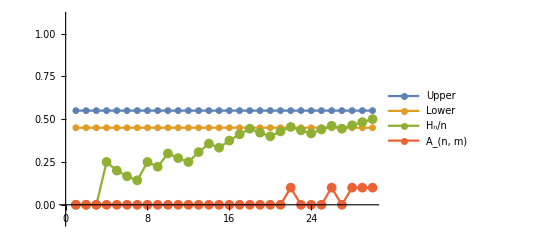

```mathematica
seqLength=30;
m=20;
data=empiricalHeadProbabilityFAST[seqLength];
upper=ConstantArray[0.5+1/m,seqLength];
lower=ConstantArray[0.5-1/m,seqLength];
setA=Boole[seqAnm[m,data]]/10;
ListPlot[{upper,lower,data,setA},PlotRange->{-0.1,1.1},Joined->True,PlotMarkers->{{"●",7},{"●",7},{"●",10},{"●",10}},PlotLegends->{"Upper","Lower","H_n/n","A_(n, m)"}]
```

Defining it as a function “sequenceAnm”:

```mathematica
seqLength=30;
m=10;
sequenceAnm[seqLength_,m_]:=Module[{},
data=empiricalHeadProbabilityFAST[seqLength];
upper=ConstantArray[0.5+1/m,seqLength];
lower=ConstantArray[0.5-1/m,seqLength];
setA=Boole[seqAnm[m,data]]/20;
dia=3;
ListPlot[{upper,lower,data,setA+.4},
PlotRange->{.4,.6},Joined->True,
PlotMarkers->{{"●",dia},{"●",dia},{"●",dia},{"●",dia}},
ImageSize->{Large},
PlotLegends->{"Upper","Lower","H_n/n","A_(n, m)"}]];
```

Let ω be an infinite coin toss sequence.  We ask the question: for m=M, is ω eventually in A_(n,M) forever?  That is, if we go out far enough (for some large N), is (H_n(ω))/n between the upper and lower M-bounds forever thereafter?

Answer: this will happen if and only if ω∈∪_(N=1)^∞∩_(n≥N)A_(n,M).

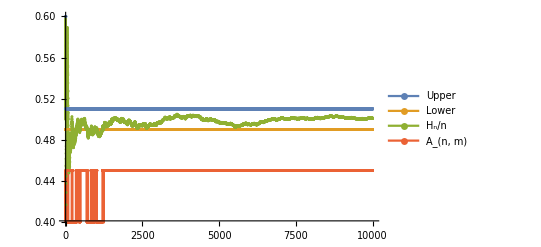

```mathematica
sequenceAnm[10000,100]
```

Question 2:

Let ω be an infinite coin toss sequence.  Write a Mathematica function that estimates the probability of ω being in the set Anm for n=100 and m=50.

Hint 1: Simulate a large number of realizations (nMonteCarlo) of the first  n tosses (you can call this nTosses) of outcomes ω using the functions defined above.  Apply the law of large numbers to derive an estimated value for this probability.  

Hint 2: Use a table of last values from a large number of runs (nMonteCarlo) of the empiricalHeadProbabilityFAST function (with nTosses input) to estimate the probability with m=50.  The function Boole[ X ] returns 1 if X is True, 0 if X is False.